```mathematica
ResourceFunction["MaTeXInstall"][]
<<MaTeX`
```

Paclet[MaTeX,1.7.9,<>]

```mathematica
(**constants**)
hbar =6.582119569*10^-16;  (* [eV*s] *)
h=4.135667696*10^-15;  (* [eV/Hz] *)
```

```mathematica
(** Parameters **)
we=0.9326;  (* [eV/hbar] *)
wc=we-20*10^-3;  (* [eV] *)
γe=67.5*10^-3;  (* [eV] *)
gamc = 1.333*10^-7*γe (*γc=2*0.9*10^-8;  (* [eV] *)*);
g=0.332*10^-3;  (* [eV] *)
v={0.0010,0.00212,0.10,0.25,0.50,1.0}*2(γe);
(* dressed parameters *)
(*Ωe[ω_]:=we - g^2(wc-ω)/((wc-ω)^2+(γc/2)^2)
Γe[ω_]:=γe + g^2(γc)/((wc-ω)^2+(γc/2)^2)
Δe[ω_]:=(Ωe[ω]-ω) - (ⅈ*Γe[ω]/2)*)
Δe[ω_]:=(we-ω)-(ⅈ*γe/2)
Δc[ω_,γc_]:=(wc-ω)-(ⅈ*γc/2)
(* Fano parameters *)
ζe[ω_]:=g^2 / ((ω-we)^2+(γe/2)^2)
Ωc[ω_]:=wc + ζe[ω]*(ω-we)
Γc[ω_]:=gamc + ζe[ω]*(γe)
```

```mathematica
gamc
```

124599.

```mathematica
ζe[wc]*(γe)
```

4.56132×10^9

```mathematica
(** calculate the average photon number **)
(*modsqβ[ω_]:=Abs[v/Δe[ω]]^2*)
modsqβ[ω_,γc_]:=Abs[(Δc[ω,γc]*v)/(Δc[ω,γc]*Δe[ω]-g^2)]^2
```

```mathematica
modsqβ[we,gamc]
modsqβ[Ωc[wc],gamc]
```

{0.000016,0.0000887364,0.16,1.,4.,16.}

{4.14313×10^-6,0.0000229779,0.0414313,0.258946,1.03578,4.14313}

```mathematica
(** calculate the average photon number transmitted through the coupled cavity **)
(* modsqα[ω_,γc_]:=modsqβ[ω,γc] / Abs[ Δc[ω,γc] ]^2 *)
modsqα[ω_,γc_]:=Abs[g* v / (Δc[ω,γc]*Δe[ω]-g^2) ]^2
modsqα[we,gamc]
modsqα[Ωc[wc],gamc]
```

{4.40896×10^-9,1.98156×10^-8,0.0000440896,0.00027556,0.00110224,0.00440896}

{0.222588,1.0004,2225.88,13911.7,55646.9,222588.}

```mathematica
(** Poisson distribution **)
p[n_,ω_]:=modsqβ[ω,gamc]^n*Exp[-modsqβ[ω,gamc]]/n!
pplt={p[n,we][[1]],
p[n,we][[2]],
p[n,we][[3]],
p[n,we][[4]]}
```

{(0.999996 (4.×10^-6)^n)/(n!),(0.999991 (9.×10^-6)^n)/(n!),(0.960789 0.04^n)/(n!),(0.778801 0.25^n)/(n!)}

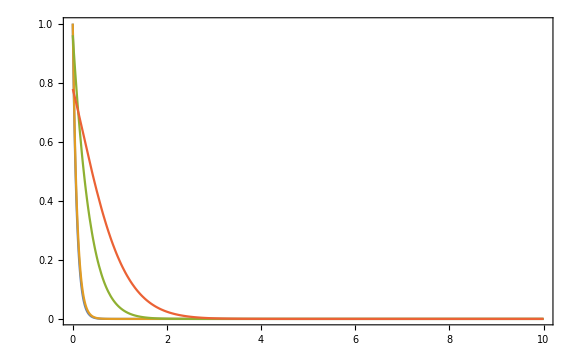

```mathematica
(** plot **)
Plot[pplt,{n,0,10},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"p(n; \\omega=\\omega_e)",None},{"n",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->{{0,10},{0,1}},
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{
"\\vert \\beta \\vert ^{2} = 0.12","\\vert \\beta \\vert ^{2} = 0.20","\\vert \\beta \\vert ^{2} = 0.04",
"\\vert \\beta \\vert ^{2} = 0.25"(*,
"\\vert \\beta \\vert ^{2} = 1",
"\\vert \\beta \\vert ^{2} = 4"*)},{0.89,0.7}],
ImageSize->Large]
```

```mathematica
pα[n_,ω_]:=modsqα[ω,gamc]^n*Exp[-modsqα[ω,gamc]]/n!
pαplt={pα[n,Ωc[wc]][[1]],
pα[n,Ωc[wc]][[2]],
pα[n,Ωc[wc]][[3]]}
```

General::munfl: Exp[-1798.52] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11240.7] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44963.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{(0.835394 0.179852^n)/(n!),(0.667199 0.404667^n)/(n!),0.}

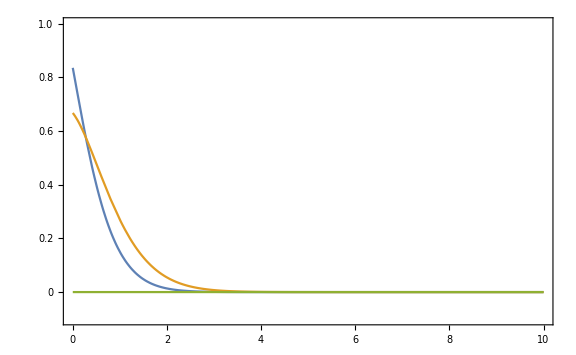

```mathematica
Plot[pαplt,{n,0,10},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"p(n; \\omega=\\omega_e)",None},{"n",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->{{0,10},{-0.1,1}},
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\vert \\alpha \\vert ^{2} = 0.04",
"\\vert \\alpha \\vert ^{2} = 0.25",
"\\vert \\alpha \\vert ^{2} = 1798"},{0.89,0.7}],
ImageSize->Large]
```

```mathematica
(** The second order correlation of light transmitted through the cavity at steady state**)
G2α[ω_,γc_]:= modsqα[ω,γc]^2
```

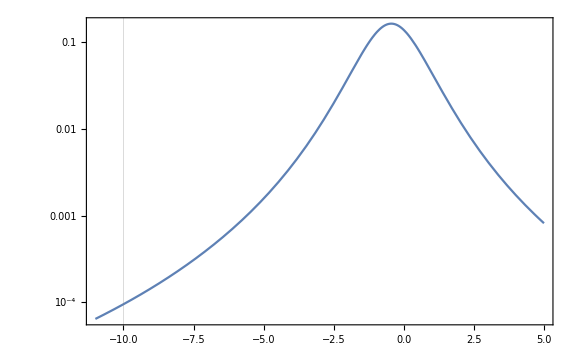

```mathematica
(* plot G2 *)
(*G2αplt=*)
(*G2α[(Δ*10^-3+Ωc[wc])];*)
LogPlot[{G2α[(Δ*10^-6+wc),gamc][[2]]},
{Δ,-11,5},
GridLines->{{{((we-20.01*10^-3)-wc)*10^6,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"\\mathrm{Log}[ G^{(2)}_{\\alpha}(\\omega)]",None},{"\\omega - \\omega_c \\: [\\mu eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
(*PlotRange->{{-11,5},{0,2.04001*10^8}},*)
PlotRange->All, Exclusions->None,
(*PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\vert \\beta \\vert ^{2} = 0.04",
"\\vert \\beta \\vert ^{2} = 0.25",
"\\vert \\beta \\vert ^{2} = 1",
"\\vert \\beta \\vert ^{2} = 4"},{0.89,0.7}],*)
ImageSize->Large]
```

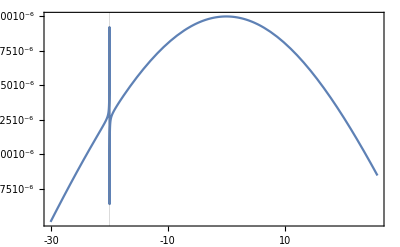

```mathematica
(** Plot average occupation number in emitter and cavity **)
Plot[(*{modsqβ[(Δ*10^-3+we),gamc][[2]]/modsqβ[(0+we),gamc][[2]],
modsqα[(Δ*10^-3+we),gamc][[2]]/modsqα[((Ωc[wc]-we)+we),gamc][[2]]},
 {Δ,-20.1,-19.9},*)
{modsqβ[(Δ*10^-3+we),gamc][[2]](*,
modsqα[(Δ*10^-3+we),gamc][[2]]*)},
 {Δ,-30.1,25.9},
GridLines->{{{(wc-we)*10^3,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"\\text{Normalized }N(\\omega)",None},{"\\omega - \\omega_e \\: [m eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
(*PlotRange->{{-3,-1},{0,9.37505*10^10}}*)
PlotRange->All, Exclusions->None
(*ImageSize->Small*)]
```

```mathematica
G2α[(-10*10^-6+wc),gamc][[2]]
```

0.0000950106

## Time dynamics

```mathematica
(*time dependent parameter*)
Δct[ω_,t_]:=Δc[ω,gamc]-g^2/Δe[ω]*(1-Exp[-ⅈ*Δe[ω]*t])
Tc[ω_]:=Re[ 2*π/Abs[ Δct[ω,Infinity]] ]
τc=(2*π)/(gamc)
```

6.98306×10^8

```mathematica
Δct[Ωc[wc],Infinity]
```

-12602.5-2.28072×10^9 ⅈ

```mathematica
Δc[Ωc[wc],gamc]-g^2/Δe[Ωc[wc]]
```

-12602.5-2.28072×10^9 ⅈ

```mathematica
2*π/Re[Δc[Ωc[wc],gamc]-g^2/Δe[Ωc[wc]]]
```

-0.000498568

```mathematica
τc*10^-2
```

6.98306×10^6

```mathematica
2*π/(1.333*10^-7*γe/2)
```

4.59634×10^-7

```mathematica
(0.9*10^-8)/(γe/2*hbar)
```

1.33333×10^-7

```mathematica
(*coherent state amplitude*)
(*coupled discrete cavity*)
α[ω_,t_]:=-g*v[[2]]/Δe[ω]*Conjugate[ (Exp[-ⅈ*Δct[ω,t]*t]-1)/Δct[ω,t] ]
(*driven broad-band emitter*)
β[ω_,t_]:=-v[[2]]/Δe[ω]*Conjugate[ 
(Exp[-ⅈ*Δe[ω]*t]-1)/Δe[ω]
+g^2/(Δe[ω]-Δct[ω,t])*
(  (Exp[-ⅈ*Δe[ω]*t]-1)/Δe[ω]
-(Exp[-ⅈ*Δct[ω,t]*t]-1)/Δct[ω,t] )
]
```

Spectrum of the Average Occupation Number

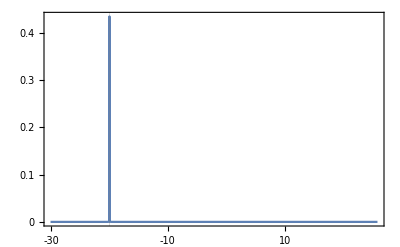

```mathematica
(* spectrum of average occupation number in the cavity*)
Plot[{Abs[α[(Δ*10^-3+we),Infinity]]^2},
 {Δ,-30.1,25.9},
GridLines->{{{(wc-we)*10^3,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{"\\text{Normalized }N(\\omega)",None},{"\\omega - \\omega_e \\: [m eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->All, Exclusions->None]
```

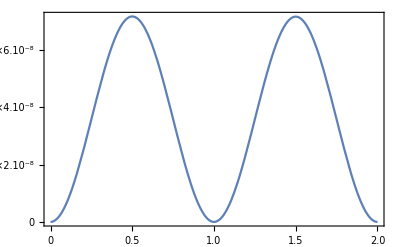

```mathematica
Plot[
Abs[  α[(1*10^-3+we),x*Tc[(1*10^-3+we)]]  ]^2,{x,0,2},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->5/3]&)/@{{"\\vert \\alpha(1 \\: \\mathrm{eV} + \\omega_e,t) \\vert^2",None},{"t \\: [T_c]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->All, Exclusions->None]
```

```mathematica
Ωc[wc]-we
```

-0.0200014

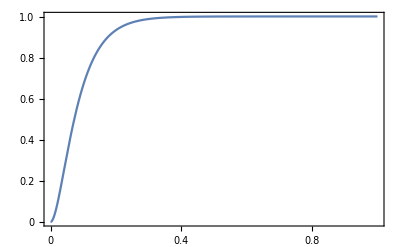

```mathematica
Plot[Abs[ (*α[(1*10^-3+we),x*10^-6*τc]*) α[(-20.0014*10^-3+we),x*10^-2*τc] ]^2,{x,0,1},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->5/3]&)/@{{"\\vert \\alpha(1 \\: \\mathrm{eV} + \\omega_e,t) \\vert^2",None},{"t \\: [10^{-2}\\times\\tau_c]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->All, Exclusions->None]
```

```mathematica
0.4*τc*10^-2*hbar
```

1.83853×10^-9

```mathematica
Abs[α[(1*10^-3/hbar+we),Infinity]]^2
```

2.24898×10^-9

```mathematica
modsqα[(1*10^-3/hbar+we),gamc][[2]]
```

2.24898×10^-9

The Second Order Correlation

```mathematica
(* second order correlation *)
G2tα[na_,ω_,t_,τ_]:= 
(na(na-1)+na(Abs[α[ω,t]]^2+Abs[α[ω,t+τ]]^2+2*Re[ Conjugate[α[ω,t]]*α[ω,t+τ] ]) +
Abs[α[ω,t]]^2*Abs[α[ω,t+τ]]^2
)/( (na+Abs[α[ω,t]]^2)(na+Abs[α[ω,t+τ]]^2) )
```

#### Plot g2(0)

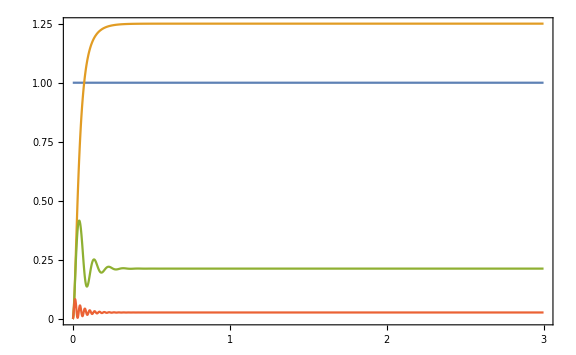

```mathematica
Plot[{G2tα[0,Ωc[wc],t*10^-2*τc,0],
G2tα[1,Ωc[wc],t*10^-2*τc,0],
G2tα[1,Ωc[wc]-4*Γc[wc]/2,t*10^-2*τc,0],
G2tα[1,Ωc[wc]-12*Γc[wc]/2,t*10^-2*τc,0]
},
{t,0,3},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->5/3]&)/@{{"G^{(2)}(\\omega,t,\\tau=0)",None},{"t \\: [10^{-2}\\times\\tau_c]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\langle a^{\\dagger}a \\rangle_{t_0} = 0, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 2\\Gamma",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 6\\Gamma"},{0.7,0.7}],
PlotRange->All, Exclusions->None,
ImageSize->Large]
```

```mathematica
G20α[na_,Δ_,t_]:=G2τα[na,(Ωc[wc]+Δ*Γc[wc]/2),t*(10^-2*τc),0]
```

```mathematica
(* Contour Plot *)
```

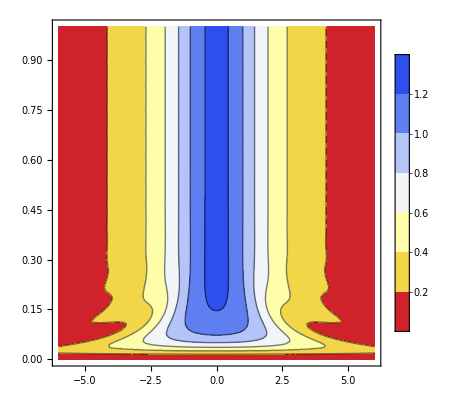

```mathematica
ContourPlot[G20α[1,Δ,t],{Δ,-6,6},{t,0,1},ColorFunction->(ColorData[{"TemperatureMap", "Reverse"}]),
PlotLegends-> Automatic,
 Exclusions->None]
```

```mathematica
ContourPlot[Sin[x] Sin[y],{x,0,3 Pi},{y,0,3 Pi},ContourShading->ColorData[35,"ColorList"]]
```

```mathematica
ContourShading->ColorData[35,"ColorList"]
```

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2,2},ColorFunction->(ColorData["TemperatureMap"][#3]&)]
```

```mathematica
Plot g2(τ)
```

```mathematica
G2τα[na_,Δ_,t_,τ_]:=G2tα[na,(Ωc[wc]-Δ*Γc[wc]/2),t,τ*10^-2*τc]
```

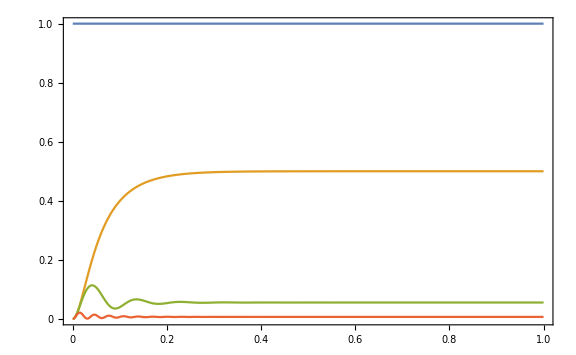

```mathematica
Plot[{G2tα[0,(Ωc[wc]-0*Γc[wc]/2),τ*10^-2*τc,0],
(*G2τα[0,0,τ],*)G2τα[1,0,0,τ],G2τα[1,4,0,τ],G2τα[1,12,0,τ]
},
{τ,0,1},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->5/3]&)/@{{"G^{(2)}(\\tau)",None},{"\\tau \\: [10^{-2}\\times\\tau_c]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\langle a^{\\dagger}a \\rangle_{t_0} = 0, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 2\\Gamma",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 6\\Gamma"},{0.7,0.7}],
PlotRange->All, Exclusions->None,
ImageSize->Large]
```

General::munfl: Exp[-235683.-139674. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

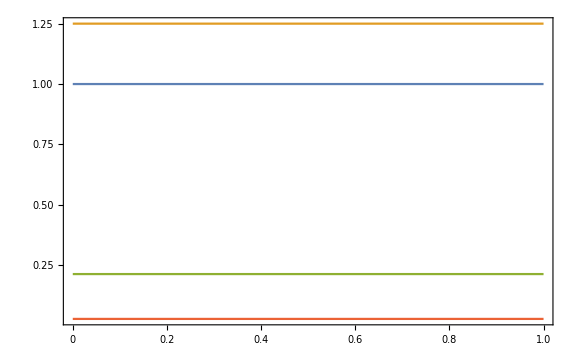

```mathematica
(** at steady state where t<<τc **)
Plot[{G2tα[0,(Ωc[wc]-0*Γc[wc]/2),τ*10^-2*τc,10^-2*τc],
(*G2τα[0,0,τ],*)G2τα[1,0,10^-2*τc,τ],G2τα[1,4,10^-2*τc,τ],G2τα[1,12,10^-2*τc,τ]
},
{τ,0,1},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->5/3]&)/@{{"G^{(2)}(\\tau)",None},{"\\tau \\: [10^{-2}\\times\\tau_c]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\langle a^{\\dagger}a \\rangle_{t_0} = 0, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 2\\Gamma",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 6\\Gamma"},{0.7,0.7}],
PlotRange->All, Exclusions->None,
ImageSize->Large]
```

### The discrete cavity that is uncoupled to the broad-band but driven directly by a laser beam

```mathematica
αc[ω_,t_]:=-(7.074*10^-14*v[[2]])/Δc[ω,gamc]*Conjugate[ 
(Exp[-ⅈ*Δc[ω,gamc]*t]-1)/Δc[ω,gamc] 
]
```

```mathematica
Abs[αc[(wc),Infinity]]^2
```

1.00058

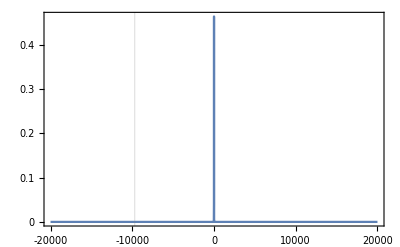

```mathematica
(* spectrum of average occupation number in the cavity*)
Plot[{Abs[αc[(Δ*10^-9+wc),Infinity]]^2},
 {Δ,-20*10^3,20*10^3},
GridLines->{{{((wc-4*Γc[wc]/2)-wc)*10^9,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{
"\\vert \\alpha_c(\\omega, t\\rightarrow\\infty) \\vert^2",None},{"\\omega - \\omega_c \\: [n eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->All, Exclusions->None]
```

#### The second order correlation of the driven, uncoupled cavity

```mathematica
(* second order correlation *)
G2αc[na_,ω_,t_,τ_]:= 
(na(na-1)+na(Abs[αc[ω,t]]^2+Abs[αc[ω,t+τ]]^2+2*Re[ Conjugate[αc[ω,t]]*αc[ω,t+τ] ]) +
Abs[αc[ω,t]]^2*Abs[αc[ω,t+τ]]^2)
g2αc[na_,ω_,t_,τ_]:= 
(na(na-1)+na(Abs[αc[ω,t]]^2+Abs[αc[ω,t+τ]]^2+2*Re[ Conjugate[αc[ω,t]]*αc[ω,t+τ] ]) +
Abs[αc[ω,t]]^2*Abs[αc[ω,t+τ]]^2
)/( (na+Abs[αc[ω,t]]^2)(na+Abs[αc[ω,t+τ]]^2) )
```

Plot g2(0)

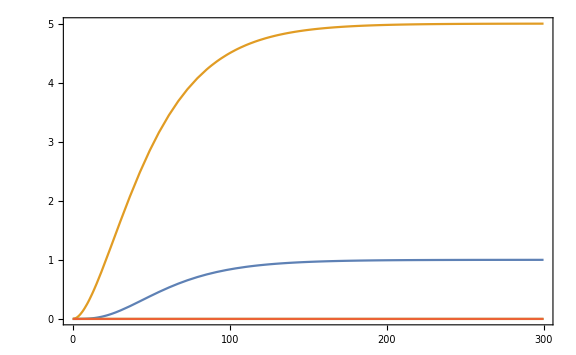

```mathematica
Plot[{G2αc[0,wc,t*10^-2*τc,0],
G2αc[1,wc,t*10^-2*τc,0],
G2αc[1,wc-4*Γc[wc]/2,t*10^-2*τc,0],
G2αc[1,Ωc[wc]-12*Γc[wc]/2,t*10^-2*τc,0]
},
{t,0,300},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->5/3]&)/@{{"G^{(2)}(\\omega,t,\\tau=0)",None},{"t \\: [10^{-2}\\times\\tau_c]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\langle a^{\\dagger}a \\rangle_{t_0} = 0, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 2\\Gamma",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 6\\Gamma"},{0.7,0.7}],
PlotRange->All, Exclusions->None,
ImageSize->Large]
```

```mathematica
Abs[αc[Ωc[wc],10^-2*τc]]^2
```

3.46959×10^-10

```mathematica
(Ωc[wc]-wc)*10^9
```

-1432.35

```mathematica
wc
```

0.9126

```mathematica
Γc[wc]/2
```

2.42159×10^-6

```mathematica
wc-4*Γc[wc]/2
```

0.91259

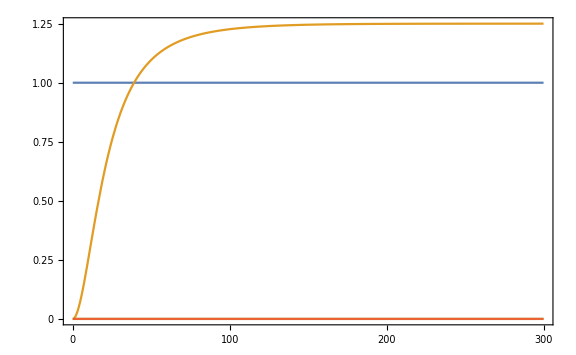

```mathematica
Plot[{g2αc[0,wc,t*10^-2*τc,0],
g2αc[1,wc,t*10^-2*τc,0],
g2αc[1,wc-4*Γc[wc]/2,t*10^-2*τc,0],
g2αc[1,wc-12*Γc[wc]/2,t*10^-2*τc,0]
},
{t,0,300},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->5/3]&)/@{{"g^{(2)}(\\omega,t,\\tau=0)",None},{"t \\: [10^{-2}\\times\\tau_c]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotLegends->Placed[(MaTeX[#,Magnification->4/3]&)/@{"\\langle a^{\\dagger}a \\rangle_{t_0} = 0, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 2\\Gamma",
"\\langle a^{\\dagger}a \\rangle_{t_0} = 1, \\omega=\\Omega_c - 6\\Gamma"},{0.7,0.7}],
PlotRange->All, Exclusions->None,
ImageSize->Large]
```

```mathematica
ζe[ω_]:=g^2 / ((ω-we)^2+(γe/2)^2)
```

```mathematica
ζe[wc]
```

0.0000716176

```mathematica
(we-wc)
```

0.02

```mathematica
gamc
```

8.99775×10^-9

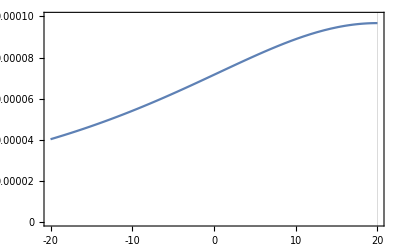

```mathematica
Plot[ζe[(Δ*10^-3+wc)],
 {Δ,-20*10^0,20*10^0},
GridLines->{{{(we-wc)*10^3,Thick}}},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{{
"\\zeta(\\omega)",None},{"\\omega - \\omega_c \\: [m eV]",None}},
BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->15},
FrameStyle->BlackFrame,
FrameTicks->All,
PlotRange->{0,10^-4}, Exclusions->None]
```

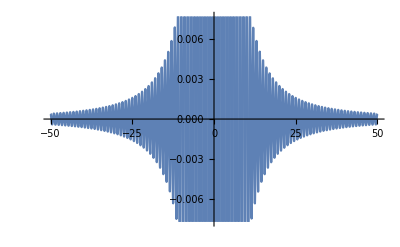

```mathematica
Functest[x_]:=Cos[2*π*x]/(x^2+1)
Plot[Functest[x],{x,-100/2,100/2}]
```